```mathematica
nbPath=NotebookDirectory[];
nbDepth=FileNameDepth[nbPath];
quiccroot=FileNameJoin[FileNameSplit[nbPath][[1;;nbDepth-4]]];
dataroot=FileNameJoin[Flatten[{quiccroot,"build","Components","SparseSM","TestSuite"}]];
If[!DirectoryQ[dataroot],
Message[dataroot::wrongpath,dataroot];
Abort[];
];
$MaxExtraPrecision=1000;
(*Worland package setup*)
pkgroot=FileNameJoin[Flatten[{quiccroot,"Components","TestSuite","Mathematica"}]];
AppendTo[$Path, pkgroot];
Worland`$mpprec=500;
Worland`$WorlandType="SphEnergy";
Needs["Worland`"];
ParallelNeeds["Worland`"]
datadir={"_data","SparseSM","Worland",$WorlandType};
refdir={"_refdata","SparseSM","Worland",$WorlandType};
```

```mathematica
spectralExpansion[i0_,iN_,l_,g_,w_,f_]:=Table[Dot[w Wnl[i,l,g], f],{i,i0,iN}];

(*(restricted) identity operator*)
id[row_,nN_,l_,gfunc_, wfunc_]:=Module[{s}, 
s=Table[If[row==i,1,0],{i,0,nN-1}];
s];
(* Integration opeators *)
r2[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p,op}, 
gN=Max[nN+Floor[l/2]+3,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= r^2 Wnl[row,l, r];
p=s/.{r->grid};
s=spectralExpansion[0,nN-1,l,grid,wgts,p];
s];
lapl[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+3,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= (1/r^2 D[r^2 D[Wnl[row,l, r],r],r]-(l(l+1))/r^2 Wnl[row,l, r])//Simplify;
p=s/.{r->grid};
If[Length@p < Length@grid,p=Table[p,Length@grid]];
s=spectralExpansion[0,nN-1,l,grid,wgts,p];
s];
lapl2[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+3,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= (1/r^2 D[r^2 D[Wnl[row,l, r],r],r]-(l(l+1))/r^2 Wnl[row,l, r])//Simplify;
s=(1/r^2 D[r^2 D[s,r],r]-(l(l+1))/r^2 s)//Simplify;
p=s/.{r->grid};
If[Length@p < Length@grid,p=Table[p,Length@grid]];
s=spectralExpansion[0,nN-1,l,grid,wgts,p];
s];
qm[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+3,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= (-D[Wnl[row,l-1, r],r]+(l-1)1/r Wnl[row,l-1, r])//Simplify;
p=s/.{r->grid};
If[Length@p < Length@grid,p=Table[p,Length@grid]];
s=spectralExpansion[0,nN-1,l,grid,wgts,p];
s];
qp[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+3,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= (D[Wnl[row,l+1, r],r]+(l+2)1/r Wnl[row,l+1, r])//Simplify;
p=s/.{r->grid};
If[Length@p < Length@grid,p=Table[p,Length@grid]];
s=spectralExpansion[0,nN-1,l,grid,wgts,p];
s];
i2[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+5,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= r^l Integrate[4 r Integrate[4 r^(1-l)Wnl[row,l, r],r],r];
p=s/.{r->grid};
s = Table[0, {i,1,nN}];
s[[2;;]]=spectralExpansion[2,nN,l,grid,wgts,p];
s];
i2lapl[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p,sf}, 
gN=Max[nN+Floor[l/2]+5,10];
grid=gfunc[gN];
wgts=wfunc[gN];
sf=(1/r^2 D[r^2 D[Wnl[row,l, r],r],r]-(l(l+1))/r^2 Wnl[row,l, r])//Simplify;
s= r^l Integrate[4 r Integrate[4 r^(1-l)sf,r],r];
p=s/.{r->grid};
If[Length@p == 0,p=Table[0,Length@grid]];
s = Table[0, {i,1,nN}];
s[[2;;]]=spectralExpansion[2,nN,l,grid,wgts,p];
s];
i2qm[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p,sf}, 
gN=Max[nN+Floor[l/2]+5,10];
grid=gfunc[gN];
wgts=wfunc[gN];
sf=(-D[Wnl[row,l-1, r],r]+(l-1)1/r Wnl[row,l-1, r])//Simplify;
s= r^l Integrate[4 r Integrate[4 r^(1-l)sf,r],r];
p=s/.{r->grid};
If[Length@p == 0,p=Table[0,Length@grid]];
s = Table[0, {i,1,nN}];
s[[2;;]]=spectralExpansion[2,nN,l,grid,wgts,p];
s];
i2qp[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p,sf}, 
gN=Max[nN+Floor[l/2]+5,10];
grid=gfunc[gN];
wgts=wfunc[gN];
sf=(D[Wnl[row,l+1, r],r]+(l+2)1/r Wnl[row,l+1, r])//Simplify;
s= r^l Integrate[4 r Integrate[4 r^(1-l)sf,r],r];
p=s/.{r->grid};
If[Length@p == 0,p=Table[0,Length@grid]];
s = Table[0, {i,1,nN}];
s[[2;;]]=spectralExpansion[2,nN,l,grid,wgts,p];
s];
i4[row_,nN_,l_, gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+8,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= r^l Integrate[4 rIntegrate[4 rIntegrate[4 r Integrate[4 r^(1-l)Wnl[row,l, r],r],r],r],r];
p=s/.{r->grid};
s = Table[0, {i,1,nN}];
s[[3;;]]=spectralExpansion[4,nN+1,l,grid,wgts,p];
s];
i4lapl[row_,nN_,l_, gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p,sf}, 
gN=Max[nN+Floor[l/2]+8,10];
grid=gfunc[gN];
wgts=wfunc[gN];
sf=(1/r^2 D[r^2 D[Wnl[row,l, r],r],r]-(l(l+1))/r^2 Wnl[row,l, r])//Simplify;
s= r^l Integrate[4 rIntegrate[4 rIntegrate[4 r Integrate[4 r^(1-l)sf,r],r],r],r];
p=s/.{r->grid};
If[Length@p == 0,p=Table[0,Length@grid]];
s = Table[0, {i,1,nN}];
s[[3;;]]=spectralExpansion[4,nN+1,l,grid,wgts,p];
s];
i4lapl[row_,nN_,l_, gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p,sf}, 
gN=Max[nN+Floor[l/2]+8,10];
grid=gfunc[gN];
wgts=wfunc[gN];
sf=(1/r^2 D[r^2 D[Wnl[row,l, r],r],r]-(l(l+1))/r^2 Wnl[row,l, r])//Simplify;
s= r^l Integrate[4 rIntegrate[4 rIntegrate[4 r Integrate[4 r^(1-l)sf,r],r],r],r];
p=s/.{r->grid};
If[Length@p == 0,p=Table[0,Length@grid]];
s = Table[0, {i,1,nN}];
s[[3;;]]=spectralExpansion[4,nN+1,l,grid,wgts,p];
s];
i4qm[row_,nN_,l_, gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p,sf}, 
gN=Max[nN+Floor[l/2]+8,10];
grid=gfunc[gN];
wgts=wfunc[gN];
sf=(-D[Wnl[row,l-1, r],r]+(l-1)1/r Wnl[row,l-1, r])//Simplify;
s= r^l Integrate[4 rIntegrate[4 rIntegrate[4 r Integrate[4 r^(1-l)sf,r],r],r],r];
p=s/.{r->grid};
If[Length@p == 0,p=Table[0,Length@grid]];
s = Table[0, {i,1,nN}];
s[[3;;]]=spectralExpansion[4,nN+1,l,grid,wgts,p];
s];
i4qp[row_,nN_,l_, gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p,sf}, 
gN=Max[nN+Floor[l/2]+8,10];
grid=gfunc[gN];
wgts=wfunc[gN];
sf=(D[Wnl[row,l+1, r],r]+(l+2)1/r Wnl[row,l+1, r])//Simplify;
s= r^l Integrate[4 rIntegrate[4 rIntegrate[4 r Integrate[4 r^(1-l)sf,r],r],r],r];
p=s/.{r->grid};
If[Length@p == 0,p=Table[0,Length@grid]];
s = Table[0, {i,1,nN}];
s[[3;;]]=spectralExpansion[4,nN+1,l,grid,wgts,p];
s];
i4lapl2[row_,nN_,l_, gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p,sf}, 
gN=Max[nN+Floor[l/2]+8,10];
grid=gfunc[gN];
wgts=wfunc[gN];
sf=(1/r^2 D[r^2 D[Wnl[row,l, r],r],r]-(l(l+1))/r^2 Wnl[row,l, r])//Simplify;
sf=(1/r^2 D[r^2 D[sf,r],r]-(l(l+1))/r^2 sf)//Simplify;
s= r^l Integrate[4 rIntegrate[4 rIntegrate[4 r Integrate[4 r^(1-l)sf,r],r],r],r];
p=s/.{r->grid};
If[Length@p == 0,p=Table[0,Length@grid]];
s = Table[0, {i,1,nN}];
s[[3;;]]=spectralExpansion[4,nN+1,l,grid,wgts,p];
s];
i6[row_,nN_,l_, gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+11,10];
grid=wgrid[gN];
wgts=wweights[gN];
s= r^l Integrate[4 r Integrate[4 r Integrate[4 rIntegrate[4 rIntegrate[4 r Integrate[4 r^(1-l)Wnl[row,l, r],r],r],r],r],r],r];
p=s/.{r->grid};
s = Table[0, {i,1,nN}];
s[[4;;]]=spectralExpansion[6,nN+2,l,grid,wgts,p];
s];
```

```mathematica
buildOperator[meta_,opfunc_,gfunc_,wfunc_]:=
Module[{outprec = 32,rows, cols,l,ref},
rows=meta[[1]];
cols=meta[[2]];
l =meta[[3]];
ref=Transpose[Table[opfunc[j,rows,l,gfunc,wfunc],{j,0,rows-1}]];
ref=SparseArray[ref];
ref
];
```

```mathematica
buildTruncatedOperator[meta_,qifunc_,taufunc_,gfunc_,wfunc_]:=
Module[{outprec = 32,opQI, opTau, opTrunc,rows, cols, l, ntrunc,ref},
rows=meta[[1]];
cols=meta[[2]];
l =meta[[3]];
ntrunc=meta[[4]];
opQI=buildOperator[meta,qifunc,gfunc,wfunc];
opTau=buildOperator[meta,taufunc,gfunc,wfunc];
opTrunc=IdentityMatrix[rows];opTrunc[[-ntrunc;;,-ntrunc;;]]= 0;
ref = SparseArray[Chop[opQI.opTrunc.opTau]];
ref
];
```

```mathematica
buildBcOperator[meta_,bcfunc_,bcRow_]:=
Module[{outprec = 32,rows, cols, l, ntrunc,ref},
rows=meta[[1]];
cols=meta[[2]];
l =meta[[3]];
ntrunc=meta[[4]];
ref=KroneckerProduct[SparseArray[{bcRow,1}->1,{rows,1}],Table[bcfunc[i,l,1],{i,0,cols-1}]];
ref
];
```

```mathematica
(* Elementary matrix for kronecker product *)
e[i_,j_,nN_]:=Module[{mat},mat=SparseArray[{i,j}->1,{nN,nN}];mat[[i,j]]=1;mat]
(* Coefficient in front of Qp, Qm *)
coeff[l_,m_]:=(l-1)(l+1)√(((l-m)(l+m))/((2l-1)(2l+1)));
(* Inverse horizontal laplacian *)
invlaplh[l_]:=1/(l(l+1));
sid[n_,k_]:=Module[{ref},
ref=IdentityMatrix[n+Abs[k]];
If[k>0,
ref=ref[[k+1;;n+k,1;;]],
ref=ref[[1;;n-k,1;;n]]];
ref
]
```

```mathematica
(* Truncation *)
m = 1;
maxL = 10;
nL=maxL-m+1;
nN=20;
```

```mathematica
(* Coriolis coupling term QP*)
Timing[
lowerQP=Table[coeff[l,m] invlaplh[l](sid[nN,1].buildTruncatedOperator[{nN+1,nN,l,1}, i2,qm,wgrid,wweights]).sid[nN,-1],{l,m+1,maxL}];
upperQP=Table[If[l>0,-coeff[l+1,m]invlaplh[l](sid[nN,1].buildTruncatedOperator[{nN+1,nN,l,1}, i2,qp,wgrid,wweights]).sid[nN,-1],0IdentityMatrix[nN]],{l,m,maxL-1}];
matLQP=Sum[KroneckerProduct[e[i+1,i,nL],lowerQP[[i]]],{i,1,nL-1}];
matUQP=Sum[KroneckerProduct[e[i,i+1,nL],upperQP[[i]]],{i,1,nL-1}];
matQP=matLQP+matUQP;
]
```

{122.12,Null}

```mathematica
(* Diagonal d/dϕ T term *)
Timing[
diagonalT=Table[If[l>0,ⅈ m invlaplh[l] (sid[nN,1].buildTruncatedOperator[{nN+1,nN,l,1}, i2,id,wgrid,wweights]).sid[nN,-1],IdentityMatrix[nN]],{l,m,maxL}];
matT = BlockDiagonalMatrix[diagonalT];
]
```

{35.6083,Null}

```mathematica
(* Coriolis coupling term QT*)
Timing[
lowerQT=Table[coeff[l,m]invlaplh[l]buildTruncatedOperator[{nN,nN,l,1}, i2,qm,wgrid,wweights],{l,m+1,maxL}];
upperQT=Table[If[l>0,-coeff[l+1,m]invlaplh[l]buildTruncatedOperator[{nN,nN,l,1}, i2,qp,wgrid,wweights],IdentityMatrix[nN]],{l,m,maxL-1}];
matLQT=Sum[KroneckerProduct[e[i+1,i,nL],lowerQT[[i]]],{i,1,nL-1}];
matUQT=Sum[KroneckerProduct[e[i,i+1,nL],upperQT[[i]]],{i,1,nL-1}];
matQT=matLQT+matUQT;
]
```

{102.352,Null}

```mathematica
(* Diagonal d/dϕ∇^2 P term *)
Timing[
diagonalP=Table[If[l>0,ⅈ m invlaplh[l]buildTruncatedOperator[{nN,nN,l,1}, i2,lapl,wgrid,wweights],IdentityMatrix[nN]],{l,m,maxL}];
bcP=Table[If[l>0,buildBcOperator[{nN,nN,l,1}, Wnl,1],0IdentityMatrix[nN]],{l,m,maxL}];
matP=BlockDiagonalMatrix[diagonalP+bcP];
]
```

{60.001,Null}

```mathematica
(* Toroidal mass matrix *)
Timing[
diagonalMT=Table[If[l>0,(sid[nN,1]. buildTruncatedOperator[{nN+1,nN,l,1}, i2,id,wgrid,wweights]).sid[nN,-1],0IdentityMatrix[nN]],{l,m,maxL}];
matMT = BlockDiagonalMatrix[diagonalMT];
]
```

{34.5788,Null}

```mathematica
(* Poloidal mass matrix *)
Timing[
diagonalMP=Table[If[l>0,buildTruncatedOperator[{nN,nN,l,1}, i2,lapl,wgrid,wweights],0IdentityMatrix[nN]],{l,m,maxL}];
matMP=BlockDiagonalMatrix[diagonalMP];
]
```

{57.097,Null}

```mathematica
(*Coriolis matrix and mass matrix*)
Timing[
matQ=KroneckerProduct[e[1,1,2],-matT] + KroneckerProduct[e[1,2,2],matQP] +KroneckerProduct[e[2,1,2],-matQT]+KroneckerProduct[e[2,2,2],-matP];
matM=KroneckerProduct[e[1,1,2],matMT] +KroneckerProduct[e[2,2,2],matMP];
]
```

{0.950577,Null}

{29.254,Null}

General::munfl: 2.375461781261493×10^-499 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -6.390014386006507×10^-500 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.291914092188866×10^-499 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

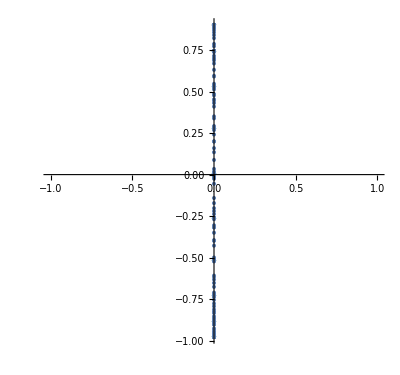

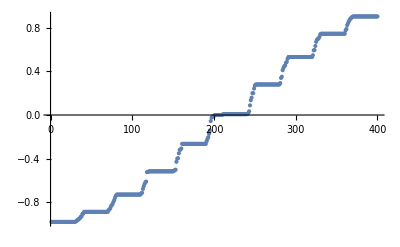

```mathematica
(* Compute eigen spectrum *)
Timing[
ev=Eigenvalues[{matQ,matM}];
If[m==0,ev=Sort[ev][[;;-(2nN+1)]]];
]
ComplexListPlot[ev]
ListPlot[Sort@Im@ev]
```

```mathematica
N[Chop@ev,5][[1;;20]]
N[Sort@Im@ev,5][[1;;20]]
N[Sort@Re@ev,5][[1;;20]]
```

{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,-0.97806 ⅈ,-0.97806 ⅈ,-0.97806 ⅈ,-0.97806 ⅈ,-0.97806 ⅈ,-0.97806 ⅈ,-0.97806 ⅈ,-0.97806 ⅈ,-0.97806 ⅈ,-0.97806 ⅈ}

{-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806,-0.97806}

{-7.0604×10^-492,-2.6914×10^-498,-2.2755×10^-498,-2.2133×10^-498,-2.186×10^-498,-1.6943×10^-498,-1.4652×10^-498,-1.2808×10^-498,-9.0257×10^-499,-8.754×10^-499,-8.6061×10^-499,-8.5883×10^-499,-8.3346×10^-499,-7.4477×10^-499,-7.289×10^-499,-7.2072×10^-499,-5.7262×10^-499,-5.0556×10^-499,-4.7514×10^-499,-4.6627×10^-499}

```mathematica
N[Chop@matQP,3]//MatrixForm
N[Chop@matT,3]//MatrixForm
N[Chop@matQT,3]//MatrixForm
N[Chop@matP,3]//MatrixForm
```

```mathematica
N[Chop@matMT,3]//MatrixForm
N[Chop@matMP,3]//MatrixForm
```

```mathematica
N[Chop@matQ,3]//MatrixForm
N[Chop@matM,3]//MatrixForm
```